# SpaceMath-Signal Strengths R_X.

## Load SpaceMath

```mathematica
<<SpaceMath`
```

SpaceMath v.1.0 | 
Documentation Centerpaclet:SpaceMath/tutorial/SpaceMathOverview | 
 | Examples
Cite |  | -Graphics-
Authors:
  ⊕ M. A. Arroyo-Ureña
 Facultad de Estudios Superiores-Cuautitlán, Universidad Nacional Autónoma de México
  ⊗ T. A. Valencia-Pérez
 Facultad de Ciencias Físico Matemáticas, Benemérita Universidad Autónoma de Puebla
 Contact us:	spacemathapp@gmail.com |

## Enter couplings

```mathematica
ghbb[Sa_,Tb_,Cb_]:=g*mb*Sqrt[1-Sa^2]/(2*mW*Tb*Cb) (* THDM-I coupling *)
```

```mathematica
(* ghbb[Sa_,Tb_,Sb_]:=-g*mb*Sa*Tb/(2*mW*Sb) *) (* THDM-II coupling *)
```

```mathematica
ghWW[Tb_,Cb_,Sb_,Sa_]:=((Tb*Cb*Sqrt[1-Sa^2])-(Sb/Tb*Sa))*(gz*mW) (* THDM-I-II coupling *)
ghZZ[Tb_,Cb_,Sb_,Sa_]:=((Tb*Cb*Sqrt[1-Sa^2])-(Sb/Tb*Sa))*(gz*mZ) (* THDM-I-II coupling *)
```

```mathematica
(***********************************************************************************)(***********************************************************************************)(***********************************************************************************)
```

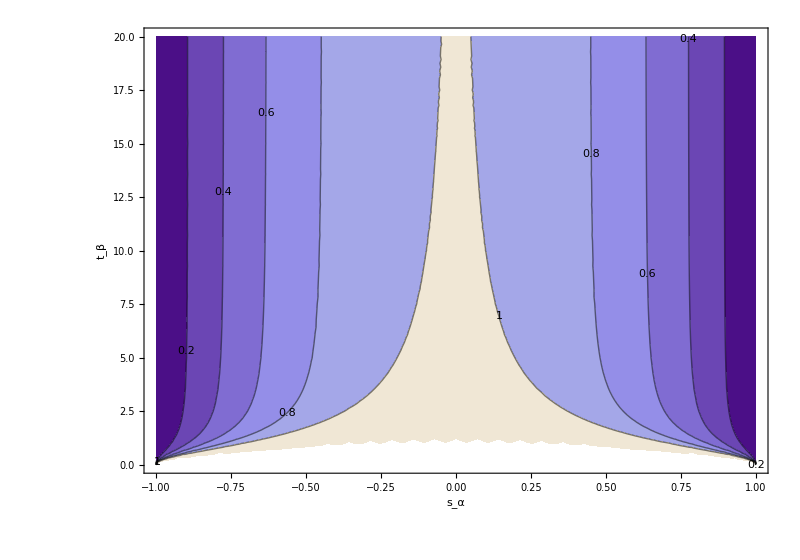

```mathematica
ContourPlot[kb[ghbb[Sa,Tb,Cos[ArcTan[Tb]]]]^2,{Sa,-1,1},{Tb,0,20},ContourLabels->True,ContourStyle->Black,Contours->{0.2,0.4,0.6,0.8,1},
ImageSize -> 800(*, ContourStyle -> {Blue, Directive[Red, Dashed]}*), 
 AxesLabel -> {Style["x", Medium, Bold, Bold], 
Style["y", Medium, Bold, Bold], Style["z", Large, Bold, Bold]}, 
 AspectRatio -> 0.7, FrameStyle -> Thickness[0.003], 
 LabelStyle -> 30,FrameLabel->{"\!\(\*SubscriptBox[\(s\), \(α\)]\)","\!\(\*SubscriptBox[\(t\), \(β\)]\)","StyleBox[\"SpaceMath\",FontWeight->\"Bold\",FontSlant->\"Italic\"]"}(*, ContourShading -> False*),ColorFunction->"LakeColors"]
```

For V = W

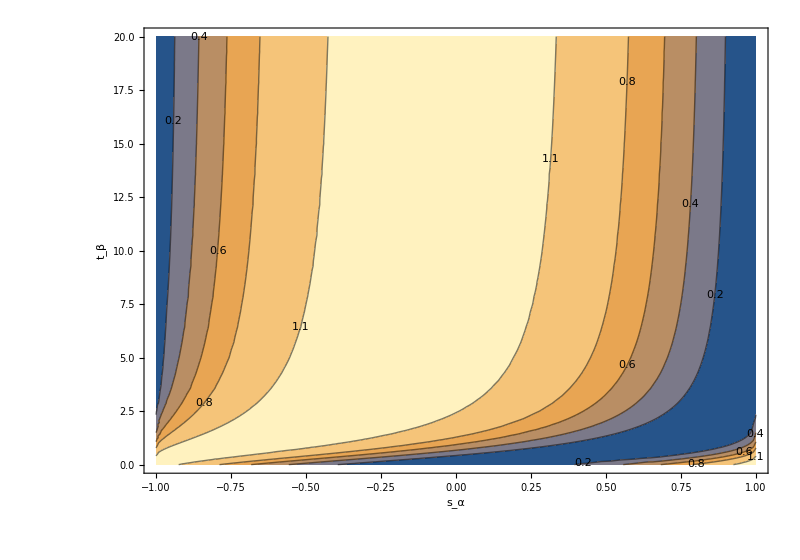

```mathematica
ContourPlot[kW[ghWW[Tb,Cos[ArcTan[Tb]],Sin[ArcTan[Tb]],Sa]]^2,{Sa,-1,1},{Tb,0,20},ContourLabels->True,ContourStyle->Black
,Contours->{0.2,0.4,0.6,0.8,1.1},
ImageSize -> 800(*, ContourStyle -> {Blue, Directive[Red, Dashed]}*), 
 AxesLabel -> {Style["x", Medium, Bold, Bold], 
Style["y", Medium, Bold, Bold], Style["z", Large, Bold, Bold]}, 
 AspectRatio -> 0.7, FrameStyle -> Thickness[0.003], 
 LabelStyle -> 30,FrameLabel->{"\!\(\*SubscriptBox[\(s\), \(α\)]\)","\!\(\*SubscriptBox[\(t\), \(β\)]\)","SpaceMath"}(*,
 ContourShading -> False*),ContourStyle->{Orange,Directive[Red,Dashed]}]
```

For V = Z

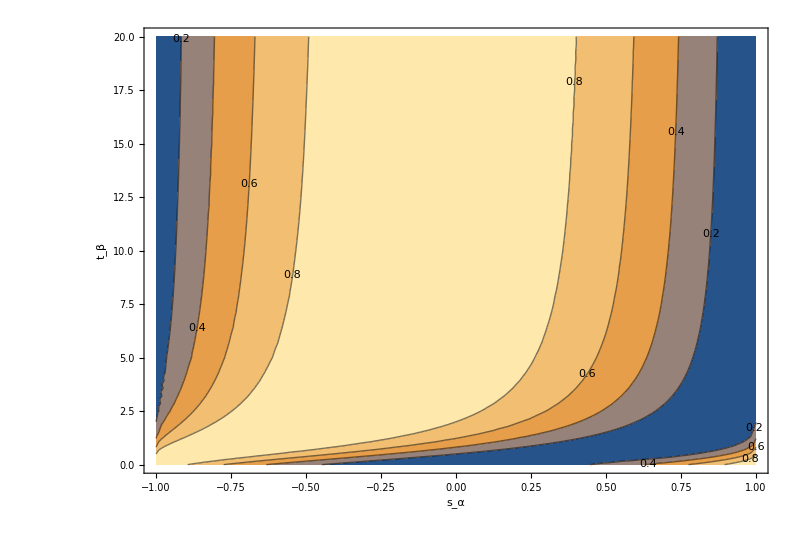

```mathematica
ContourPlot[kZ[ghZZ[Tb,Cos[ArcTan[Tb]],Sin[ArcTan[Tb]],Sa]]^2,{Sa,-1,1},{Tb,0,20},ContourLabels->True,ContourStyle->Black
,Contours->{0.2,0.4,0.6,0.8,1.1},
ImageSize -> 800(*, ContourStyle -> {Blue, Directive[Red, Dashed]}*), 
 AxesLabel -> {Style["x", Medium, Bold, Bold], 
Style["y", Medium, Bold, Bold], Style["z", Large, Bold, Bold]}, 
 AspectRatio -> 0.7, FrameStyle -> Thickness[0.003], 
 LabelStyle -> 30,FrameLabel->{"\!\(\*SubscriptBox[\(s\), \(α\)]\)","\!\(\*SubscriptBox[\(t\), \(β\)]\)","SpaceMath"}(*,
 ContourShading -> False*),ContourStyle->{Orange,Directive[Red,Dashed]}]
```